## 01 : RandomInk

1. BSplineCurve (weight, control points)
     close point not through
     average trajectory
     
    A  line could go through all of the points, but the degree could also be infinite.(y=a*x^1+b)
     
     BsplineCurve could with same points and different degree

2. BezierCurve (3D surface)

```mathematica
cpts=Table[{RandomInteger[{0,10}],RandomInteger[{0,10}]},10]
```

{{2,3},{6,7},{2,10},{8,0},{6,5},{2,8},{2,7},{4,2},{8,7},{1,1}}

Tips: *     *     temporary command

```mathematica
Graphics[{Point[cpts],BSplineCurve[cpts,SplineKnots->"Clamped",SplineClosed->True]}]
Clear[RandomInk]
```

-Graphics-

Module
scoping of constraining, 
define things locally,
following
everything, compact final function, local valuable  -> not kill any value before

```mathematica
Module[{ttt},ttt=10;]
```

Tips:    @    shortcut for function
            Last@FindShortestTour[Points]    =     Last[FindShourtestTour[Points] ]
            f[x]=f@x
            While 
            loop
            FindShortestTour
            Append
            add some function at the end of the list

## polygon是用来填充图案的命令

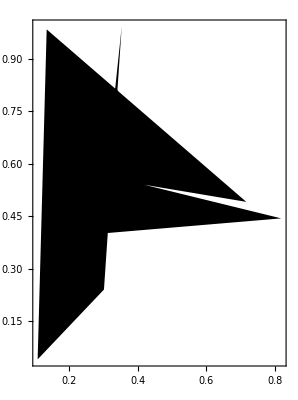

```mathematica
points=RandomReal[{0,1},{8,2}];
Graphics[Polygon[points],Frame->True]
```

## BSplineFunction类似纯函数，它的语法是自变量放在后面

```mathematica
Clear[points];
points=RandomReal[{0,1},{8,2}]
```

{{0.155803,0.849766},{0.684095,0.249912},{0.992379,0.877771},{0.557215,0.600328},{0.239851,0.202701},{0.087732,0.272883},{0.00210128,0.418367},{0.814632,0.768953}}

```mathematica
BSplineFunction[points]
```

BSplineFunction[…]

```mathematica
BSplineFunction[points][0]
```

{0.155803,0.849766}

```mathematica
BSplineFunction[points][1]
```

{0.814632,0.768953}

```mathematica
BSplineFunction[points][0.5]
```

{0.40443,0.408757}

```mathematica
BSplineFunction[points][0.68]
```

{0.185205,0.249194}

## 这个函数可以得到最短距离和点的顺序排列

```mathematica
FindShortestTour[points]
```

{2.92925,{1,4,8,3,2,5,6,7,1}}

```mathematica
Last@FindShortestTour[points]
```

{1,4,8,3,2,5,6,7,1}

```mathematica
Append[Last@FindShortestTour[points],1]
```

{1,4,8,3,2,5,6,7,1,1}

## 根据顺序重新生成点阵

```mathematica
points[[Append[Last@FindShortestTour[points],1]]]
```

{{0.155803,0.849766},{0.557215,0.600328},{0.814632,0.768953},{0.992379,0.877771},{0.684095,0.249912},{0.239851,0.202701},{0.087732,0.272883},{0.00210128,0.418367},{0.155803,0.849766},{0.155803,0.849766}}

```mathematica
Table[BSplineFunction[points][a],{a,0,1,0.001}];这个命令可以从0-1间隔0.001找点
```

## 接下来定义函数

```mathematica
Clear[RandomInk,x,y,points,a];
RandomInk[x_,y__]:=
Module[{points},points =RandomReal[{0,1},{x,2}];

points=points[[Append[Last@FindShortestTour[points],1]]];

Graphics[{RandomColor[],
Polygon@Table[BSplineFunction[points][a],{a,0,1,0.001}]},y]]
```

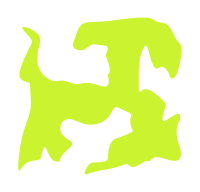

```mathematica
RandomInk[100,ImageSize->200]
```

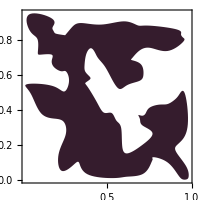
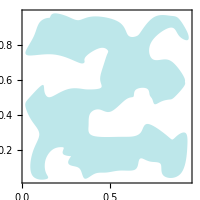
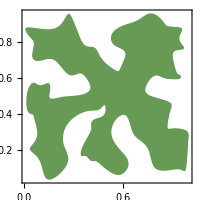
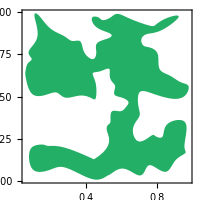
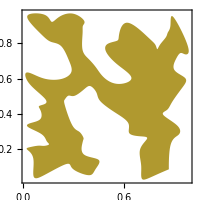
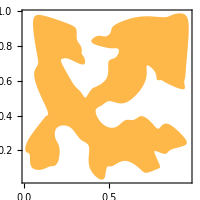
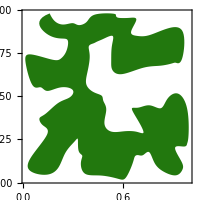
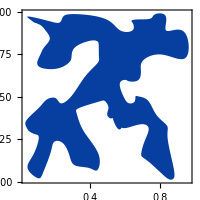

```mathematica
Table[RandomInk[100,ImageSize->200,AspectRatio->1,Frame->True],8]
```

```mathematica
Clear[RandomInk,x,y,points,a];
RandomInk[x_,y__]:=
Module[{points},points =RandomReal[{0,1},{x,2}];

points=points[[Append[Last@FindShortestTour[points],1]]];

Graphics[{RandomColor[],Polygon[
aaa=Table[BSplineFunction[points][a],{a,0,1,0.001}]],
Red, Point/@aaa, Orange, Circle[#,Total[#]/20]&/@
(Table[aaa[[i]],{i,1,Length[aaa],4}])},y]]
```

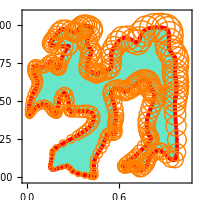

```mathematica
RandomInk[100,ImageSize->200,AspectRatio->1,Frame->True]
```

```mathematica
RandomReal[{0,1},{10,2}]
```

{{0.30814,0.285065},{0.0912016,0.604839},{0.546565,0.0758828},{0.536918,0.323081},{0.606118,0.0599792},{0.0306686,0.347121},{0.626036,0.0781078},{0.363649,0.46733},{0.0455258,0.715785},{0.546489,0.514045}}

```mathematica
RandomReal[{0,1},{10,2,3}]
```

{{{0.217817,0.534625,0.925139},{0.467649,0.338862,0.413228}},{{0.973636,0.0267523,0.631179},{0.76696,0.932241,0.281306}},{{0.116071,0.635571,0.209666},{0.436566,0.0650375,0.202768}},{{0.153986,0.361181,0.353216},{0.886399,0.195742,0.568647}},{{0.293866,0.565063,0.585581},{0.0314178,0.899502,0.546871}},{{0.628874,0.540194,0.600239},{0.432142,0.364347,0.204553}},{{0.281922,0.471951,0.282882},{0.234184,0.468243,0.313312}},{{0.880055,0.0470996,0.0660519},{0.405417,0.329094,0.703313}},{{0.913274,0.449591,0.856236},{0.91793,0.315349,0.986688}},{{0.283629,0.240919,0.831982},{0.0909902,0.359185,0.650432}}}

## 还可以拓展到3维

```mathematica
Clear[RandomInk,x,y,points,a];
RandomInk[x_,y__]:=
Module[{points},
points =Flatten[RandomReal[{0,1},{x,2,3}],1];

points=points[[Append[Last@FindShortestTour[points],1]]];

Graphics3D[{RandomColor[],Polygon[
aaa=Table[BSplineFunction[points][a],{a,0,1,0.001}]],
Red, Point/@aaa, Orange, Sphere[#,Total[#]/50]&/@
(bbb=Table[aaa[[i]],{i,1,Length[aaa],4}])},y]]
```

```mathematica
RandomInk[100,ImageSize->200,AspectRatio->1,Frame->True]
```

-Graphics3D-

## 还可以暂时隐藏polygon

```mathematica
Clear[RandomInk,x,y,points,a,aaa,bbb];
RandomInk[x_,y__]:=
Module[{points},
points =Flatten[RandomReal[{0,1},{x,2,3}],1];

points=points[[Append[Last@FindShortestTour[points],1]]];

Graphics3D[{aaa=Table[BSplineFunction[points][a],{a,0,1,0.001}],
(*Polygon[aaa]*),
Red,Point/@aaa,Orange,
Sphere[#,Total[#]/50]&/@
(bbb=Table[aaa[[i]],{i,1,Length[aaa],4}])},y]]
```

```mathematica
RandomInk[100,ImageSize->200,AspectRatio->1,Frame->True];
```

## 我们回到平面研究，这一次，要取消掉所有靠的太近的点。

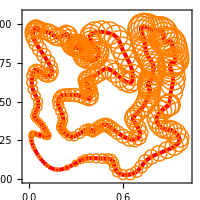

```mathematica
Clear[RandomInk,x,y,points,aaa,bbb];
RandomInk[x_,y__]:=
Module[{points},points =RandomReal[{0,1},{x,2}];

points=points[[Append[Last@FindShortestTour[points],1]]];

Graphics[{RandomColor[],aaa=Table[BSplineFunction[points][a],{a,0,1,0.001}];
(*Polygon[aaa]*),
Red, Point/@aaa, Orange, Circle[#,Total[#]/20]&/@
(Table[aaa[[i]],{i,1,Length[aaa],4}])},y]];
graphPlot=RandomInk[100,ImageSize->200,AspectRatio->1,Frame->True]
```

```mathematica
Length[aaa]
```

1001

```mathematica
Norm用来求解距离
```

```mathematica
Select[aaa,Norm[(#-aaa[[1]])]>0.8&];
```

```mathematica
tttt=Table[Select[aaa,Norm[(#-aaa[[i]])]>0.8&],{i,100,200}]
Length[%]
```

{{{0.334147,0.298859},{0.325486,0.293176},{0.316663,0.287633},{0.307786,0.282515},{0.298964,0.278109},{0.290306,0.274699},{0.281919,0.272571},203,{0.806895,0.154308},{0.81944,0.159867},{0.832286,0.165257},{0.845301,0.170554},{0.858354,0.175832},{0.871316,0.181168}},99,{1}}
 |  |  |  |

101

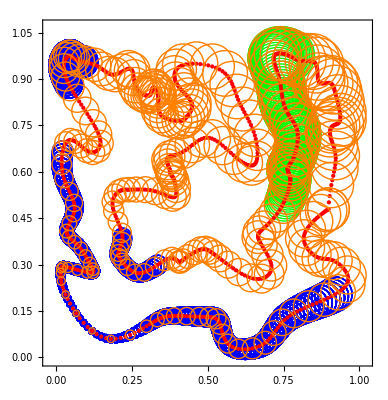

```mathematica
Show[Graphics[{Blue,Circle[#,Total[#]/20]&/@Flatten[tttt,1],
Green,Circle[#,Total[#]/20]&/@Take[aaa,{100,200}]}],
graphPlot,Frame->True]
```